```mathematica
(*How can seeded deterministic generator give rise to intermittent multiscale processes *)
```

```mathematica
{{ClearAll[caStep,caUniform,caGaussian,standardize,ar1,dyadicField,generateMarket];

(*1. Deterministic Rule-30 engine*)
caStep[state_List,rule_Integer:30]:=MapThread[BitGet[rule,4 #1+2 #2+#3]&,{RotateRight[state],state,RotateLeft[state]}];
caUniform[n_Integer?Positive,seed_Integer,width_Integer:127,burnIn_Integer:512]:=Module[{state,bits=53},state=IntegerDigits[Abs[seed]+1,2,width];
Do[state=caStep[state],{burnIn}];
Table[state=caStep[state];
(FromDigits[Take[RotateLeft[state,Mod[37 t+seed,width]],bits],2]+1/2)/2^bits,{t,n}]//N];
caGaussian[n_,seed_]:=Sqrt[2.] InverseErf[2 caUniform[n,seed]-1];

(*2. Temporal and multiscale components*)(_□)_□standardize[x_List]:=(x-Mean[x])/StandardDeviation[x];
ar1[x_List,persistence_]:=Rest@FoldList[persistence #1+Sqrt[1-persistence^2] #2&,0.,x];
dyadicField[n_,scale_,seed_,persistence_]:=Module[{coarse},coarse=caGaussian[Ceiling[n/scale]+2,seed];
coarse=standardize@ar1[coarse,persistence];
standardize@Take[Flatten[ConstantArray[#,scale]&/@coarse],n]];

(*3. Turbulence core plus market adapter*)
generateMarket[n_Integer?Positive,seed_Integer,levels_Integer:9,intermittency_:0.35,persistence_:0.70,annualizedVolatility_:0.20,initialPrice_:100.]:=Module[{innovations,fields,logVolatility,relativeVolatility,dailyVolatility,returns,logPrices},innovations=standardize@caGaussian[n,seed+7919];
fields=Table[dyadicField[n,2^(level-1),seed+104729 level,persistence],{level,levels}];
logVolatility=intermittency Total[fields]/Sqrt[levels];
relativeVolatility=Exp[logVolatility];
relativeVolatility/=Mean[relativeVolatility];
dailyVolatility=annualizedVolatility/Sqrt[252.];
(* returns=dailyVolatility standardize[relativeVolatility innovations]; *)
scaleToRMS[x_List,target_]:=target x/Sqrt[Mean[x^2]];
       returns=scaleToRMS[relativeVolatility innovations,dailyVolatility];
logPrices=Log[initialPrice]+Accumulate[returns];
<|"Returns"->returns,"Prices"->Exp[logPrices],"LogPrices"->logPrices,"Volatility"->dailyVolatility relativeVolatility,"Innovation"->innovations,"LogVolatility"->logVolatility,"ScaleFields"->fields|>];}, {□}}
```

{{Null^8 (Null_□)_□},{□}}

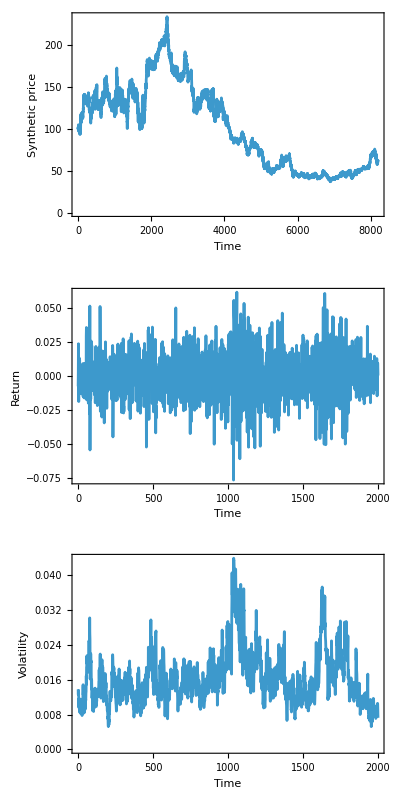

```mathematica
(*Running scenario above*)
market=generateMarket[8192,20260817,10,0.38,0.72];
GraphicsGrid[{{ListLinePlot[market["Prices"],Frame->True,FrameLabel->{"Time","Synthetic price"}]},{ListLinePlot[Take[market["Returns"],2000],PlotRange->All,Frame->True,FrameLabel->{"Time","Return"}]},{ListLinePlot[Take[market["Volatility"],2000],PlotRange->All,Frame->True,FrameLabel->{"Time","Volatility"}]}}]
```

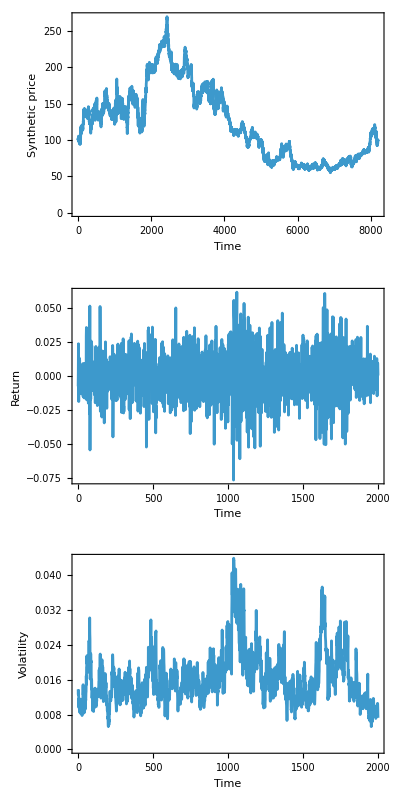

```mathematica
(*Exact reproducability results check*)
market2=generateMarket[8192,20260817,10,0.38,0.72];(_□)_(((□_□)_□)_□)market["Returns"]===market2["Returns"]
```